```mathematica
ClearAll["Global`*"]
LaplaceTransform[Sin[ω*t],t,s]
LaplaceTransform[Sin[ω*(t-τ)],t,s]
LaplaceTransform[1,t,s]
LaplaceTransform[1-τ,t,s]
LaplaceTransform[UnitStep[t-K*dt]-UnitStep[t-(K+1)*dt],t,s]
```

ω/(s^2+ω^2)

(ω Cos[τ ω]-s Sin[τ ω])/(s^2+ω^2)

1/s

(1-τ)/s

(UnitStep[-dt K]+ⅇ^(-dt K s) UnitStep[dt K])/s-(UnitStep[-dt (1+K)]+ⅇ^(-dt (1+K) s) UnitStep[dt (1+K)])/s

```mathematica
(*p.103からの状態方程式に基づくレギュレータの設計を参考にする．*)
```

### ２次遅れ要素 k/(1+s T)，kは出力を大きくするだけ．Tは応答速度を増減させる．

```mathematica
(*u[t]は，(T*f''[t]+f[t])/k*)
ClearAll["Global`*"]
Leq=Simplify@LaplaceTransform[(f''[t]+2*ζ*ωn*f'[t]+ωn^2*f[t])/(K*ωn^2),t,s]/.{f[0]->0,f'[0]->0};
Print["ラプラス変換 L[eq]= ",Leq]
G[s_]=1/Coefficient[Leq,LaplaceTransform[f[t],t,s]];(*伝達関数*)
Print["伝達関数G=L[eq]/L[f]=",G[s]]
repl={ωn->5,K->1};
```

ラプラス変換 L[eq]= ((s^2+2 s ζ ωn+ωn^2) LaplaceTransform[f[t],t,s])/(K ωn^2)

伝達関数G=L[eq]/L[f]=(K ωn^2)/(s^2+2 s ζ ωn+ωn^2)

#### 連続入力に対する応答

(ⅇ^(-t (ζ ωn+√((-1+ζ^2) ωn^2))) (-1+ⅇ^(2 t √((-1+ζ^2) ωn^2))) K ωn^2)/(2 √((-1+ζ^2) ωn^2))

(5 ⅇ^(-5 t (ζ+√(-1+ζ^2))) (-1+ⅇ^(10 t √(-1+ζ^2))))/(2 √(-1+ζ^2))

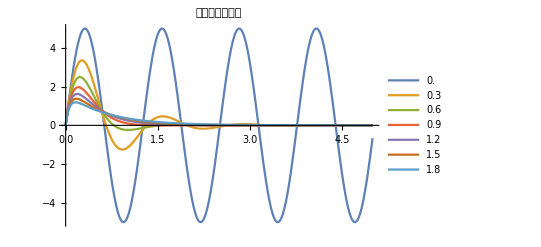

-(ⅇ^(-t (ζ ωn+√((-1+ζ^2) ωn^2))) K ((-1+ⅇ^(2 t √((-1+ζ^2) ωn^2))) ζ ωn+(1+ⅇ^(2 t √((-1+ζ^2) ωn^2))-2 ⅇ^(t (ζ ωn+√((-1+ζ^2) ωn^2)))) √((-1+ζ^2) ωn^2)))/(2 √((-1+ζ^2) ωn^2))

(ⅇ^(-5 t (ζ+√(-1+ζ^2))) (ζ-ⅇ^(10 t √(-1+ζ^2)) ζ-(1+ⅇ^(10 t √(-1+ζ^2))-2 ⅇ^(5 t (ζ+√(-1+ζ^2)))) √(-1+ζ^2)))/(2 √(-1+ζ^2))

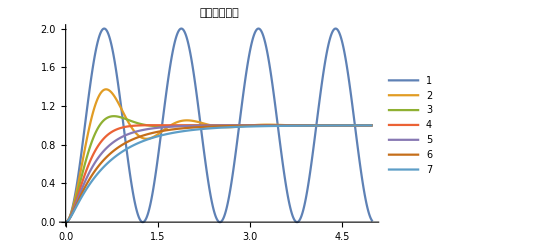

1/(2 √((-1+ζ^2) ωn^2) (1+(-2+4 ζ^2) ωn^2+ωn^4))ⅇ^(-t (ζ ωn+√((-1+ζ^2) ωn^2))) K ωn^2 (-1+ⅇ^(2 t √((-1+ζ^2) ωn^2))+ωn^2-ⅇ^(2 t √((-1+ζ^2) ωn^2)) ωn^2-2 ζ^2 ωn^2+2 ⅇ^(2 t √((-1+ζ^2) ωn^2)) ζ^2 ωn^2+2 ζ ωn √((-1+ζ^2) ωn^2)+2 ⅇ^(2 t √((-1+ζ^2) ωn^2)) ζ ωn √((-1+ζ^2) ωn^2)-4 ⅇ^(t (ζ ωn+√((-1+ζ^2) ωn^2))) ζ ωn √((-1+ζ^2) ωn^2) Cos[t]+2 ⅇ^(t (ζ ωn+√((-1+ζ^2) ωn^2))) √((-1+ζ^2) ωn^2) (-1+ωn^2) Sin[t])

(5 ⅇ^(-5 t (ζ+√(-1+ζ^2))) (12-12 ⅇ^(10 t √(-1+ζ^2))-25 ζ^2+25 ⅇ^(10 t √(-1+ζ^2)) ζ^2+25 ζ √(-1+ζ^2)+25 ⅇ^(10 t √(-1+ζ^2)) ζ √(-1+ζ^2)-50 ⅇ^(5 t (ζ+√(-1+ζ^2))) ζ √(-1+ζ^2) Cos[t]+120 ⅇ^(5 t (ζ+√(-1+ζ^2))) √(-1+ζ^2) Sin[t]))/(4 √(-1+ζ^2) (144+25 ζ^2))

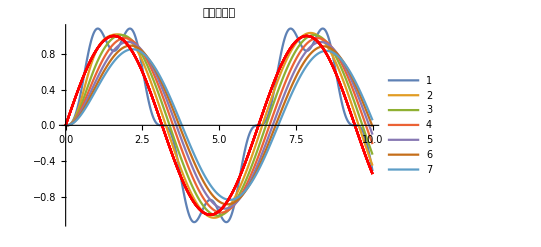

1/(2 √((-1+ζ^2) ωn^2))K (ⅇ^(-1. (-0.6+t) (ζ ωn+√((-1+ζ^2) ωn^2))) ((-1+ⅇ^(2. (-0.6+1. t) √((-1+ζ^2) ωn^2))) ζ ωn+(1+ⅇ^(2. (-0.6+1. t) √((-1+ζ^2) ωn^2))-2 ⅇ^(1. (-0.6+t) (ζ ωn+√((-1+ζ^2) ωn^2)))) √((-1+ζ^2) ωn^2)) HeavisideTheta[-0.6+t]-ⅇ^(-1. (-0.4+t) (ζ ωn+√((-1+ζ^2) ωn^2))) ((-1+ⅇ^(2. (-0.4+1. t) √((-1+ζ^2) ωn^2))) ζ ωn+(1+ⅇ^(2. (-0.4+1. t) √((-1+ζ^2) ωn^2))-2 ⅇ^(1. (-0.4+t) (ζ ωn+√((-1+ζ^2) ωn^2)))) √((-1+ζ^2) ωn^2)) HeavisideTheta[-0.4+t])

1/(10 √(-1+ζ^2))(5 ⅇ^(-5. (-0.6+t) (ζ+√(-1+ζ^2))) ((-1+ⅇ^(10. (-0.6+1. t) √(-1+ζ^2))) ζ+(1+ⅇ^(10. (-0.6+1. t) √(-1+ζ^2))-2 ⅇ^(5. (-0.6+t) (ζ+√(-1+ζ^2)))) √(-1+ζ^2)) HeavisideTheta[-0.6+t]-5 ⅇ^(-5. (-0.4+t) (ζ+√(-1+ζ^2))) ((-1+ⅇ^(10. (-0.4+1. t) √(-1+ζ^2))) ζ+(1+ⅇ^(10. (-0.4+1. t) √(-1+ζ^2))-2 ⅇ^(5. (-0.4+t) (ζ+√(-1+ζ^2)))) √(-1+ζ^2)) HeavisideTheta[-0.4+t])

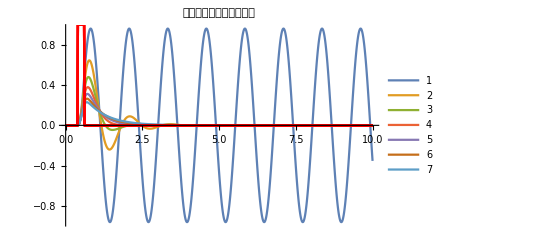

```mathematica
(*インパルス応答*)
U[s_,ω_]=1;
y[t_]=Simplify@InverseLaplaceTransform[G[s]*U[s,ω],s,t]
y[t_]=Simplify[y[t]/.repl]
tab=Table[Table[{t,y[t]/.repl},{t,0,5,.01}],{ζ,0,2,.3}];
ListPlot[tab,Joined->True,PlotRange->All,PlotLabel->"インパルス応答",PlotLegends->Table[ζ,{ζ,0,2,.3}]]

(*ステップ応答*)
u[t_]=1;
U[s_,ω_]=LaplaceTransform[u[t],t,s];
y[t_]=Simplify@InverseLaplaceTransform[G[s]*U[s,ω],s,t]
y[t_]=Simplify[y[t]/.repl]
input=ParallelTable[Table[{t,u[t]},{t,0,5,.01}],{ζ,0,2,.3}];
res=ParallelTable[Table[{t,y[t]},{t,0,5,.01}],{ζ,0,2,.3}];
ListPlot[res,Joined->True,PlotLegends->Automatic,PlotRange->All,PlotLabel->"ステップ応答"]

(*周波数応答*)
ω=1;
u[t_,ω_]=Sin[ω*t];
U[s_,ω_]=LaplaceTransform[u[t,ω],t,s];
y[t_]=Simplify@InverseLaplaceTransform[G[s]*U[s,ω],s,t]
y[t_]=Simplify[y[t]/.repl/.ω->1]
Show[
ListPlot[ParallelTable[Table[{t,y[t]},{t,0,10,.01}],{ζ,0,2,.3}],Joined->True,PlotLegends->Automatic,PlotRange->All,PlotLabel->"周波数応答"],
ListPlot[ParallelTable[Table[{t,u[t,ω]/.ω->1},{t,0,10,.01}],{ζ,0,2,.3}],Joined->True,PlotLegends->Automatic,PlotRange->All,PlotStyle->Red]
]

(*ステップ２応答*)
ω=1;
u[t_]=UnitStep[t-K*dt]-UnitStep[t-(K+1)*dt]/.{K->2,dt->.2};
U[s_,ω_]=LaplaceTransform[u[t],t,s];
y[t_]=Simplify@InverseLaplaceTransform[G[s]*U[s,ω],s,t]
y[t_]=Simplify[y[t]/.repl]
Show[
ListPlot[ParallelTable[Table[{t,y[t]},{t,0,10,.01}],{ζ,0,2,.3}],Joined->True,PlotLegends->Automatic,PlotRange->All,PlotLabel->"孤立矩形波に対する応答"],
ListPlot[ParallelTable[Table[{t,u[t]},{t,0,10,.01}],{ζ,0,2,.3}],Joined->True,PlotLegends->Automatic,PlotRange->All,PlotStyle->Red]
]
```

-0.745113 UnitStep[-10.1+t]-0.200899 UnitStep[-10.+t]-0.0515448 UnitStep[-9.9+t]+0.105948 UnitStep[-9.8+t]+0.246713 UnitStep[-9.7+t]+0.348528 UnitStep[-9.6+t]+0.395318 UnitStep[-9.5+t]+0.379696 UnitStep[-9.4+t]+0.304129 UnitStep[-9.3+t]+0.180546 UnitStep[-9.2+t]+0.0284586 UnitStep[-9.1+t]-0.128121 UnitStep[-9.+t]-0.264474 UnitStep[-8.9+t]-0.359072 UnitStep[-8.8+t]-0.39698 UnitStep[-8.7+t]-0.372214 UnitStep[-8.6+t]-0.288684 UnitStep[-8.5+t]-0.159576 UnitStep[-8.4+t]-0.00527536 UnitStep[-8.3+t]+0.149858 UnitStep[-8.2+t]+0.281333 UnitStep[-8.1+t]+0.368391 UnitStep[-8.+t]+0.397288 UnitStep[-7.9+t]+0.363463 UnitStep[-7.8+t]+0.272254 UnitStep[-7.7+t]+0.138063 UnitStep[-7.6+t]-0.0179259 UnitStep[-7.5+t]-0.171084 UnitStep[-7.4+t]-0.297232 UnitStep[-7.3+t]-0.376454 UnitStep[-7.2+t]-0.396241 UnitStep[-7.1+t]-0.353471 UnitStep[-7.+t]-0.254896 UnitStep[-6.9+t]-0.116078 UnitStep[-6.8+t]+0.041066 UnitStep[-6.7+t]+0.191727 UnitStep[-6.6+t]+0.312118 UnitStep[-6.5+t]+0.383233 UnitStep[-6.4+t]+0.393843 UnitStep[-6.3+t]+0.342275 UnitStep[-6.2+t]+0.236669 UnitStep[-6.1+t]+0.0936976 UnitStep[-6.+t]-0.0640661 UnitStep[-5.9+t]-0.211715 UnitStep[-5.8+t]-0.325939 UnitStep[-5.7+t]-0.388704 UnitStep[-5.6+t]-0.390102 UnitStep[-5.5+t]-0.329911 UnitStep[-5.4+t]-0.217634 UnitStep[-5.3+t]-0.0709977 UnitStep[-5.2+t]+0.0868476 UnitStep[-5.1+t]+0.230982 UnitStep[-5.+t]+0.338649 UnitStep[-4.9+t]+0.392851 UnitStep[-4.8+t]+0.38503 UnitStep[-4.7+t]+0.316422 UnitStep[-4.6+t]+0.197857 UnitStep[-4.5+t]+0.0480556 UnitStep[-4.4+t]-0.109333 UnitStep[-4.3+t]-0.24946 UnitStep[-4.2+t]-0.350203 UnitStep[-4.1+t]-0.395657 UnitStep[-4.+t]-0.378645 UnitStep[-3.9+t]-0.301853 UnitStep[-3.8+t]-0.177406 UnitStep[-3.7+t]-0.0249496 UnitStep[-3.6+t]+0.131446 UnitStep[-3.5+t]+0.267088 UnitStep[-3.4+t]+0.360564 UnitStep[-3.3+t]+0.397114 UnitStep[-3.2+t]+0.370969 UnitStep[-3.1+t]+0.286256 UnitStep[-3.+t]+0.156349 UnitStep[-2.9+t]+0.0017585 UnitStep[-2.8+t]-0.15311 UnitStep[-2.7+t]-0.283805 UnitStep[-2.6+t]-0.369694 UnitStep[-2.5+t]-0.397217 UnitStep[-2.4+t]-0.362027 UnitStep[-2.3+t]-0.269682 UnitStep[-2.2+t]-0.134759 UnitStep[-2.1+t]+0.0214386 UnitStep[-2.+t]+0.174252 UnitStep[-1.9+t]+0.299555 UnitStep[-1.8+t]+0.377564 UnitStep[-1.7+t]+0.395965 UnitStep[-1.6+t]+0.351851 UnitStep[-1.5+t]+0.252188 UnitStep[-1.4+t]+0.11271 UnitStep[-1.3+t]-0.0445625 UnitStep[-1.2+t]-0.1948 UnitStep[-1.1+t]-0.314282 UnitStep[-1.+t]-0.384146 UnitStep[-0.9+t]-0.393362 UnitStep[-0.8+t]-0.340475 UnitStep[-0.7+t]-0.233834 UnitStep[-0.6+t]-0.0902762 UnitStep[-0.5+t]+0.0675345 UnitStep[-0.4+t]+0.214683 UnitStep[-0.3+t]+0.327938 UnitStep[-0.2+t]+0.389418 UnitStep[-0.1+t]

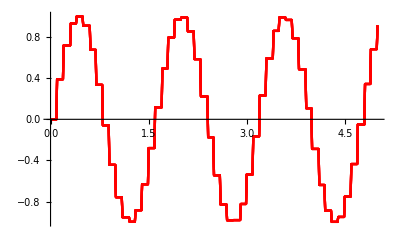

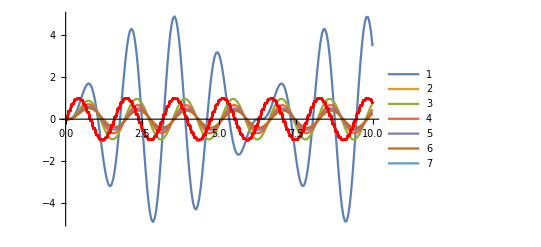

```mathematica
(*ステップ２応答*)
ω=4;
u[t_]=FullSimplify@Sum[Sin[ω*(K*dt)](UnitStep[t-K*dt]-UnitStep[t-(K+1)*dt])/.{dt->.1},{K,0,100,1}]
ListPlot[Table[Table[{t,u[t]},{t,0,5,.01}],{ζ,0,2,.3}],Joined->True,PlotLegends->Automatic,PlotRange->All,PlotStyle->Red]

U[s_,ω_]=LaplaceTransform[u[t],t,s];
y[t_]=InverseLaplaceTransform[G[s]*U[s,ω],s,t]/.repl;
Show[
ListPlot[ParallelTable[Table[{t,y[t]},{t,0,10,.05}],{ζ,0,2,.3}],Joined->True,PlotLegends->Automatic,PlotRange->All],
ListPlot[ParallelTable[Table[{t,u[t]/.ω->1},{t,0,10,.05}],{ζ,0,2,.3}],Joined->True,PlotLegends->Automatic,PlotRange->All,PlotStyle->Red]
]
```

#### 離散入力に対する応答

(UnitStep[-0.05 K]+ⅇ^(-0.05 K s) UnitStep[0.05 K])/s-(UnitStep[-0.05 (1+K)]+ⅇ^(-0.05 (1+K) s) UnitStep[0.05 (1+K)])/s

```mathematica
(*周波数応答*)
U[s_,ω_]:=ω/(s^2+ω^2);(*入力を離散化しなければならない*)
U[s_,ω_,dt_]:=LaplaceTransform[Sin[0.05 ω *step[t,dt]],t,s]
dt=0.1;
y[t_]=Simplify@InverseLaplaceTransform[G[s]*U[s,ω,dt],s,t]

y[t_]=Simplify[y[t]/.repl/.ω->1]
dt=.05
ListPlot[Table[Table[{t,y[dt*Floor[t/dt]]},{t,0,5,.01}],{ζ,0,2,.3}],Joined->True,PlotLegends->Automatic,PlotRange->All]
```

K ωn^2 InverseLaplaceTransform[LaplaceTransform[Sin[0.2 step[t,0.1]],t,s]/(s^2+2 s ζ ωn+ωn^2),s,t]

25 InverseLaplaceTransform[LaplaceTransform[Sin[0.2 step[t,0.1]],t,s]/(25+s^2+10 s ζ),s,t]

0.05

$Aborted

```mathematica
Get["https://raw.githubusercontent.com/faysou/MTools/master/BootstrapInstall.m"]
Needs["MTools`"]
```

ProjectInstaller not found, installing it:

/Users/tomoaki/Library/Mathematica/Applications/ProjectInstaller

Installing MTools:

/Users/tomoaki/Library/Mathematica/Applications/MTools

```mathematica
TestClass=NewClass["Fields"->{"a","b"}]
testObject=New[TestClass][]
testObject.a=1
testObject.a
```

TestClass

TestClass[object$250211]

1

1

```mathematica
実際をどのように　シミュレーションするか？
```

### 1次遅れ要素 k/(1+s T)，kは出力を大きくするだけ．Tは応答速度を増減させる．

```mathematica
(*u[t]は，(T*f''[t]+f[t])/k*)
ClearAll["Global`*"]
Lu=Simplify@LaplaceTransform[(T*f'[t]+f[t])/k,t,s]/.{f[0]->0,f'[0]->0}
Zu=Simplify@ZTransform[(T*f'[t]+f[t])/k,t,s]/.{f[0]->0,f'[0]->0}
G[s_]=1/Coefficient[Lu,LaplaceTransform[f[t],t,s]](*伝達関数*)
GZ[s_]=1/Coefficient[Zu,ZTransform[f[t],t,s]](*伝達関数*)
```

((1+s T) LaplaceTransform[f[t],t,s])/k

(ZTransform[f[t],t,s]+T ZTransform[f'[t],t,s])/k

k/(1+s T)

k

```mathematica
(*インパルス応答*)
```

(ⅇ^(-t/T) k)/T

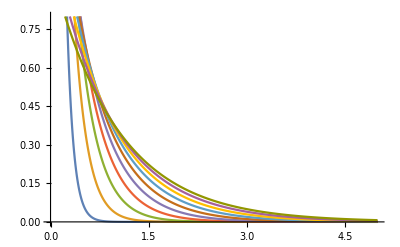

(1-ⅇ^(-t/T)) k

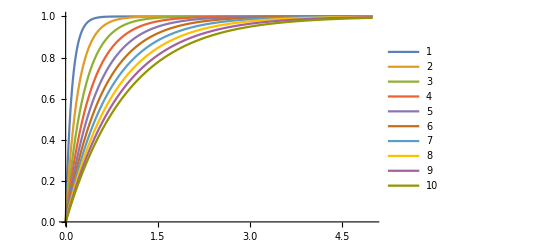

k ω ((ⅇ^(-t/T) T)/(1+T^2 ω^2)+(-T ω Cos[t ω]+Sin[t ω])/(ω (1+T^2 ω^2)))

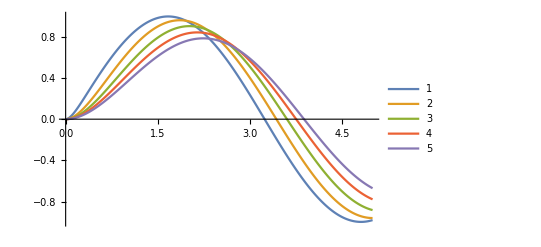

(k (-T)^(1-t) UnitStep[-1+t])/T

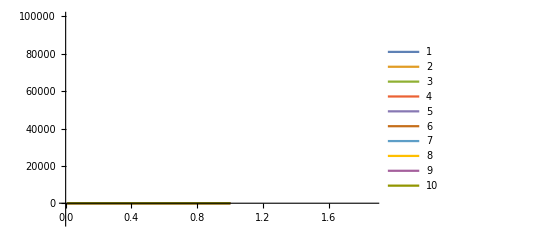

```mathematica
U[s_,ω_]:=1;
y[t_]=InverseLaplaceTransform[G[s]*U[s,ω],s,t]
ListPlot[Table[Table[{t,y[t]/.{k->1}},{t,0,5,.01}],{T,.1,1,.1}],Joined->True]

(*ステップ応答*)
U[s_,ω_]:=1/s;
y[t_]=InverseLaplaceTransform[G[s]*U[s,ω],s,t]
ListPlot[Table[Table[{t,y[t]/.{k->1}},{t,0,5,.01}],{T,.1,1,.1}],Joined->True,PlotLegends->Automatic]

(*周波数応答*)
U[s_,ω_]:=ω/(s^2+ω^2);
y[t_]=InverseLaplaceTransform[G[s]*U[s,ω],s,t]
ListPlot[Table[Table[{t,y[t]/.{ω->1,k->1}},{t,0,5,.01}],{T,.1,1,.2}],Joined->True,PlotLegends->Automatic]

(*ステップ応答2*)
U[s_,ω_]:=1;
y[t_]=InverseZTransform[G[s]*U[s,ω],s,t]
ListPlot[Table[Table[{t,y[t]/.{k->1}},{t,0.01,5,.01}],{T,.1,1,.1}],Joined->True,PlotLegends->Automatic]
```

```mathematica
y[t_]=InverseLaplaceTransform[G[s]*INPUT[s],s,t]
これを離散的に表現してプログラムすれば良いだろう．
```

k InverseLaplaceTransform[INPUT[s]/(1+s T),s,t]

． これを離散的に表現してプログラムすれば良いだろう

```mathematica
tmp=InverseZTransform[G[s]*U[s,1],s,z]/.{T->1.,k->1}
ListPlot[Table[{z,tmp},{z,0,10,.02}]]
```

InverseZTransform[U[s,1.]/(1.+s),s,z]

-Graphics-